g2 graph 21b
level 3

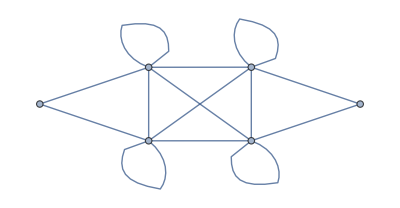

```mathematica
SetDirectory["~/Documents/UNH/Research/code/github/graph_21b"];
graph = { 
{0,1,0,0,0,1},
{1,1,1,0,1,1},
{0,1,1,1,1,1},
{0,0,1,0,1,0},
{0,1,1,1,1,1},
{1,1,1,0,1,1}
 };
AdjacencyGraph[ graph] (* picture of the graph *)
Clear[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
SetNonCommutative[aa,bb,cc,dd,ee,ff,gg,hh,ii,jj,kk,ll,mm,nn,oo,pp,qq,rr,ss,tt,uu,vv,ww,xx];
CGamma = { 
{0,aa,0,0,0,bb},
{cc,dd,ee,0,ff,gg},
{0,hh,ii,jj,kk,ll},
{0,0,mm,0,nn,0},
{0,oo,pp,qq,rr,ss},
{tt,uu,vv,0,ww,xx}
};
level=4;
q=Exp[Pi*I/(3*(4+level))]; (* see physics paper *)
```

Data import

```mathematica
linearEqns = Import["./data/linearEqns.m"];
linearSol = Solve[linearEqns][[1]];
bigonEqns = Import["./data/bigonEqns.m"];
trigonEqns = Import["./data/trigonEqns.m"];
traceEqns = Import["./data/traceEqns.m"];
reducedLoEqns = Import["./data/reducedLo.m"];
squareEqns = Import["./data/squareEqns.m"];
pentEqns = Import["./data/pentEqns.m"];
```

```mathematica
hiEqns = Join[squareEqns, pentEqns];
Parallelize[
reducedHiEqns = Map[Simplify, hiEqns/.linearSol]
]
```

{2 (5+2 √6) alpha69^4+(49+20 √6) alpha8^4==71+16 √2+13 √3+29 √6+(27+11 √2+9 √3+11 √6) alpha8^2,2 alpha69^2 (-3-√2-√3-√6+(5+2 √6) alpha8^2+(5+2 √6) alpha85^2)==22+5 √2+4 √3+9 √6,2 alpha69^2 (-3-√2-√3-√6+(5+2 √6) alpha8^2+(5+2 √6) alpha85^2)==22+5 √2+4 √3+9 √6,2122,alpha73^2 alpha78^2 alpha87+alpha88+(1+alpha64^2) alpha74^2 alpha88+alpha86 (1+(1+alpha11^2) alpha74^2-√(-2+√6) alpha85 alpha88-alpha87 alpha88)==alpha86^2 alpha88^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88),alpha73^2 alpha74^2 alpha86+alpha88+(1+alpha64^2) alpha78^2 alpha88+alpha87 (1+(1+alpha33^2) alpha78^2-√(-2+√6) alpha85 alpha88-alpha86 alpha88)==alpha87^2 alpha88^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88),alpha74^4 alpha86+alpha78^4 alpha87+alpha88 (3+2 alpha64^2+alpha64^4+2 alpha88^2)==(√(-2+√6) alpha85+alpha86+alpha87+alpha88) (alpha88^2+alpha88^4)}
 |  |  |  |

```mathematica
loVariables=Union@Cases[reducedLoEqns,_Symbol,Infinity];
loVariables = DeleteCases[loVariables, True];
loVariables = DeleteCases[loVariables, Pi]
loVariables//Length
```

{alpha10,alpha11,alpha30,alpha31,alpha32,alpha33,alpha50,alpha55,alpha61,alpha62,alpha63,alpha64,alpha69,alpha73,alpha74,alpha78,alpha8,alpha85,alpha86,alpha87,alpha88,alpha9}

22

```mathematica
loVariables=Union@Cases[reducedHiEqns,_Symbol,Infinity];
loVariables = DeleteCases[loVariables, True];
loVariables = DeleteCases[loVariables, Pi]
loVariables//Length
```

{alpha10,alpha11,alpha30,alpha31,alpha32,alpha33,alpha50,alpha55,alpha61,alpha62,alpha63,alpha64,alpha69,alpha73,alpha74,alpha78,alpha8,alpha85,alpha86,alpha87,alpha88,alpha9}

22

Scratch work.

```mathematica
reducedLoEqns//TableForm
```

True
1/6 (-3+√3+√6) (alpha69^2+(1+√(3/2)) alpha8^2)==1
1/6 (-3+√3+√6) (alpha69^2+(1+√(3/2)) alpha85^2)==1
(-3+√3+√6) alpha69^2+((3-√3+√6) alpha8^2)/(√2)==6
1/6 (-3+√3+√6) (alpha10^2+alpha11^2+alpha8^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^2)==1
1/6 (-3+√3+√6) (alpha30^2+alpha50^2+alpha73^2+alpha9^2)==1
1/6 (-3+√3+√6) (alpha10^2+alpha50^2+alpha61^2+alpha74^2)==1
1/6 (-3+√3+√6) (alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2)==1
1/6 (-3+√3+√6) (alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2)==1
((3-√3+√6) (alpha31^2+alpha55^2))/(√2)==6
1/6 (-3+√3+√6) (alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2)==1
1/6 (-3+√3+√6) (alpha33^2+alpha73^2+alpha78^2+alpha87^2)==1
((3-√3+√6) (alpha31^2+alpha55^2))/(6 √2)==1
((3-√3+√6) (alpha55^2+alpha63^2))/(6 √2)==1
((3-√3+√6) (alpha55^2+alpha63^2))/(√2)==6
1/6 (-3+√3+√6) (alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2)==1
1/6 (-3+√3+√6) (alpha64^2+alpha74^2+alpha78^2+alpha88^2)==1
(-3+√3+√6) alpha69^2+((3-√3+√6) alpha85^2)/(√2)==6
1/6 (-3+√3+√6) (alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2)==1
(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha8^2)==27+6 √2+5 √3+11 √6
(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha8^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha8^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha31^2+alpha55^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha31^2+alpha55^2)==2 (3+√3+√6)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)
alpha11 alpha69^2+√(1+√(3/2)) (1+√3) alpha8==(1+√(3/2)) alpha8^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
(1+√3) alpha69+√(1+√(3/2)) alpha69 (alpha11 alpha8+alpha85 alpha86)==0
alpha69^2 alpha86==1/2 √(1+√(3/2)) alpha85 (-2 (1+√3)+2 alpha85^2+√(2 (2+√6)) alpha85 (alpha86+alpha87+alpha88))
alpha10^3+alpha11^3+√(1+√(3/2)) alpha8^3+alpha9^3==alpha10+alpha11+√(-2+√6) alpha8+alpha9+√3 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^3
√(1+√(3/2)) ((-2+√6) alpha11 alpha69^2-alpha8^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9))==-((1+√3) alpha8)
alpha10 alpha50^2+alpha11 alpha73^2+(1+√3+alpha30^2) alpha9==alpha9^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha10 (1+√3+alpha61^2)+alpha11 alpha74^2+alpha50^2 alpha9==alpha10^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha10 alpha74^2+√(-2+√6) alpha69^2 alpha8+alpha11 (1+√3+alpha86^2)+alpha73^2 alpha9==alpha11^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha10 alpha50^2+alpha11 alpha73^2+(1+√3+alpha30^2) alpha9==alpha9^2 (alpha10+alpha11+√(-2+√6) alpha8+alpha9)
alpha32 alpha50^2+alpha33 alpha73^2+alpha30 (1+√3+alpha9^2)==alpha30^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
alpha73 alpha74 alpha78+alpha50 (1+√3+alpha30 alpha32+alpha61 alpha62+alpha10 alpha9)==0
alpha50 alpha74 alpha78+alpha73 (1+√3+alpha30 alpha33+alpha86 alpha87+alpha11 alpha9)==0
(1+√3+alpha10^2) alpha61+alpha50^2 alpha62+alpha64 alpha74^2==alpha61^2 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)
alpha50 alpha73 alpha78+alpha74 (1+√3+alpha10 alpha11+alpha61 alpha64+alpha86 alpha88)==0
alpha69 ((1+√3) √(-2+√6)+alpha11 alpha8+alpha85 alpha86)==0
√(-2+√6) alpha69^2 alpha85+(1+√3+alpha11^2) alpha86+alpha73^2 alpha87+alpha74^2 alpha88==alpha86^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)
alpha30^3+√(1+√(3/2)) alpha31^3+alpha32^3+alpha33^3==alpha30+√(-2+√6) alpha31+alpha32+alpha33+√3 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^3
√(1+√(3/2)) (-alpha31^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)+alpha32 alpha55^2)==-((1+√3) alpha31)
alpha30 alpha50^2+√(1+√(3/2)) alpha31 alpha55^2+alpha32 (1+√3+alpha62^2)+alpha33 alpha78^2==alpha32^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
alpha30 alpha73^2+alpha32 alpha78^2+alpha33 (1+√3+alpha87^2)==alpha33^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
√(2+√6) (3+√2+√3+√6) alpha31+(5+2 √6) alpha32 alpha55^2==(5+2 √6) alpha31^2 (alpha30+√(-2+√6) alpha31+alpha32+alpha33)
alpha55 (2 (1+√3)+√(2 (2+√6)) (alpha31 alpha32+alpha62 alpha63))==0
√(1+√(3/2)) alpha55 (alpha31 alpha32+alpha62 alpha63)==-((1+√3) alpha55)
alpha50^2 alpha61+(1+√3+alpha32^2) alpha62+√(1+√(3/2)) alpha55^2 alpha63+alpha64 alpha78^2==alpha62^2 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)
alpha50 alpha73 alpha74+alpha78 (1+√3+alpha32 alpha33+alpha62 alpha64+alpha87 alpha88)==0
alpha73^2 alpha86+(1+√3+alpha33^2) alpha87+alpha78^2 alpha88==alpha87^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)
(-1+√(3/2)) ((5+2 √6) alpha55^2 alpha62+√(22+9 √6) alpha63 (1+√3-alpha63^2-√(1+√(3/2)) alpha63 (alpha61+alpha62+alpha64)))==0
alpha61^3+alpha62^3+√(1+√(3/2)) alpha63^3+alpha64^3==alpha61+alpha62+√(-2+√6) alpha63+alpha64+√3 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^3
√(1+√(3/2)) (alpha55^2 alpha62-alpha63^2 (alpha61+alpha62+√(-2+√6) alpha63+alpha64))==-((1+√3) alpha63)
alpha61 alpha74^2+alpha62 alpha78^2+alpha64 (1+√3-alpha64 (alpha61+alpha62+√(-2+√6) alpha63+alpha64)+alpha88^2)==0
alpha74^2 alpha86+alpha78^2 alpha87+alpha88 (1+√3+alpha64^2-alpha88 (√(-2+√6) alpha85+alpha86+alpha87+alpha88))==0
(5+2 √6) alpha85^2 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)==(1+√3) √(22+9 √6) alpha85+(2+√6) alpha69^2 alpha86
√(1+√(3/2)) alpha85^3+alpha86^3+alpha87^3+alpha88^3==√(-2+√6) alpha85+alpha86+alpha87+alpha88+√3 (√(-2+√6) alpha85+alpha86+alpha87+alpha88)+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^3
alpha85^2 (2 alpha85+√(2 (2+√6)) (alpha86+alpha87+alpha88))==2 (alpha85+√3 alpha85+√(-2+√6) alpha69^2 alpha86)

Begin 5/22 work.

```mathematica
bigonEqns//Length
trigonEqns//Length
traceEqns//Length
squareEqns//Length
pentEqns//Length
```

24

88

24

384

1744

```mathematica
bigonEqns/.linearSol//FullSimplify//DeleteDuplicates//TableForm
```

(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha8^2)==27+6 √2+5 √3+11 √6
(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha8^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha8+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha8^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha31^2+alpha55^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha31^2+alpha55^2)==2 (3+√3+√6)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)

```mathematica
(3+√3+√6)/(√2)//Sqrt//N
```

2.25347

```mathematica
bigonEqns/.linearSol/.alpha8->alpha85//FullSimplify//DeleteDuplicates//TableForm
```

(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha85^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha85+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha31^2+alpha32^2+alpha33^2+(alpha30+√(-2+√6) alpha31+alpha32+alpha33)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha31^2+alpha55^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha31^2+alpha55^2)==2 (3+√3+√6)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)

```mathematica
bigonEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63//FullSimplify//DeleteDuplicates//TableForm
```

(√2+√3) ((2+√6) alpha69^2+(5+2 √6) alpha85^2)==27+6 √2+5 √3+11 √6
alpha10^2+alpha11^2+alpha85^2+alpha9^2+(alpha10+alpha11+√(-2+√6) alpha85+alpha9)^2==(3+√3+√6)/(√2)
√(-2+√6) alpha69^2+√(1+√(3/2)) alpha85^2==√6 (2+√3)^(1/4)
alpha30^2+alpha50^2+alpha73^2+alpha9^2==(3+√3+√6)/(√2)
alpha10^2+alpha50^2+alpha61^2+alpha74^2==(3+√3+√6)/(√2)
alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2==(3+√3+√6)/(√2)
alpha30^2+alpha32^2+alpha33^2+alpha63^2+(alpha30+alpha32+alpha33+√(-2+√6) alpha63)^2==(3+√3+√6)/(√2)
√(2+√6) (alpha55^2+alpha63^2)==2 √3 (2+√3)^(1/4)
alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2==(3+√3+√6)/(√2)
alpha33^2+alpha73^2+alpha78^2+alpha87^2==(3+√3+√6)/(√2)
2 (√2+√3) (alpha55^2+alpha63^2)==2 (3+√3+√6)
alpha61^2+alpha62^2+alpha63^2+alpha64^2+(alpha61+alpha62+√(-2+√6) alpha63+alpha64)^2==(3+√3+√6)/(√2)
alpha64^2+alpha74^2+alpha78^2+alpha88^2==(3+√3+√6)/(√2)
alpha85^2+alpha86^2+alpha87^2+alpha88^2+(√(-2+√6) alpha85+alpha86+alpha87+alpha88)^2==(3+√3+√6)/(√2)

```mathematica
Parallelize[
Map[RootReduce,trigonEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
]//DeleteDuplicates//TableForm
```

alpha11 alpha69^2+1/2 (2+√6) alpha85^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha85 Root2.58Root[-9-12 #1^2+2 #1^4&,2]2.583454008527105+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha69 (1+√3+alpha11 alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha85 alpha86 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
alpha69^2 alpha86+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1+√3+alpha85 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
-alpha10+alpha10^3-alpha11+alpha11^3-alpha9+alpha9^3+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha85^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
((-2+√6) alpha11 alpha69^2+alpha85^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha85
alpha10 alpha50^2+alpha11 alpha73^2+alpha9 (1+√3+alpha30^2+alpha9 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858))==0
alpha10+√3 alpha10+alpha10 alpha61^2+alpha11 alpha74^2+alpha50^2 alpha9+alpha10^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha11+√3 alpha11+alpha10 alpha74^2+alpha11 alpha86^2+alpha73^2 alpha9+alpha11^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha69^2 alpha85 Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858==0
alpha10 alpha50^2+alpha11 alpha73^2+alpha9+√3 alpha9+alpha30^2 alpha9+alpha9^2 (-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha30+√3 alpha30+alpha32 alpha50^2+alpha33 alpha73^2+alpha30 alpha9^2+alpha30^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha73 alpha74 alpha78+alpha50 (1+√3+alpha30 alpha32+alpha61 alpha62+alpha10 alpha9)==0
alpha50 alpha74 alpha78+alpha73 (1+√3+alpha30 alpha33+alpha86 alpha87+alpha11 alpha9)==0
alpha61+√3 alpha61+alpha10^2 alpha61+alpha50^2 alpha62+alpha64 alpha74^2+alpha61^2 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
alpha50 alpha73 alpha78+alpha74 (1+√3+alpha10 alpha11+alpha61 alpha64+alpha86 alpha88)==0
alpha69 (alpha11 alpha85+alpha85 alpha86)==alpha69 Root-1.83Root[64-256 #1^2-48 #1^4+32 #1^6+#1^8&,1]-1.8316760398869047
alpha86+√3 alpha86+alpha11^2 alpha86+alpha73^2 alpha87+alpha74^2 alpha88+alpha86^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha69^2 alpha85 Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858==0
-alpha30+alpha30^3-alpha32+alpha32^3-alpha33+alpha33^3+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha63^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
(alpha32 alpha55^2+alpha63^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha63
alpha32+√3 alpha32+alpha30 alpha50^2+alpha32 alpha62^2+alpha33 alpha78^2+alpha32^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha55^2 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha33+√3 alpha33+alpha30 alpha73^2+alpha32 alpha78^2+alpha33 alpha87^2+alpha33^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
1/2 (2+√6) alpha32 alpha55^2+1/2 (2+√6) alpha63^2 (-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha63 Root2.58Root[-9-12 #1^2+2 #1^4&,2]2.583454008527105+alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha55 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1+√3+alpha32 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha62 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
alpha55 (alpha32 alpha63+alpha62 alpha63) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha55
alpha50^2 alpha61+alpha62+√3 alpha62+alpha32^2 alpha62+alpha64 alpha78^2+alpha62^2 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha55^2 alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
alpha50 alpha73 alpha74+alpha78 (1+√3+alpha32 alpha33+alpha62 alpha64+alpha87 alpha88)==0
alpha73^2 alpha86+alpha87+√3 alpha87+alpha33^2 alpha87+alpha78^2 alpha88+alpha87^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)==0
1/2 (2+√6) alpha55^2 alpha62+alpha63 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 (1+√3+alpha63 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142)==0
-alpha61+alpha61^3-alpha62+alpha62^3-alpha64+alpha64^3+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha63^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
(alpha55^2 alpha62+alpha63^2 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha63
alpha61 alpha74^2+alpha62 alpha78^2+alpha64 (1+√3+alpha88^2+alpha64 (-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858))==0
alpha74^2 alpha86+alpha78^2 alpha87+alpha88 (1+√3+alpha64^2+alpha88 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858))==0
alpha69^2 alpha86+1/2 (2+√6) alpha85^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+alpha85 Root2.58Root[-9-12 #1^2+2 #1^4&,2]2.583454008527105+alpha85 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
-alpha86+alpha86^3-alpha87+alpha87^3-alpha88+alpha88^3+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858+√3 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)+(-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^3+alpha85^3 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==0
((-2+√6) alpha69^2 alpha86+alpha85^2 (-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)) Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142==(-1-√3) alpha85

```mathematica
Parallelize[
Map[RootReduce,traceEqns/.linearSol/.alpha8->alpha85/.alpha31->alpha63]
]//DeleteDuplicates//TableForm
```

(alpha69^2+1/2 (2+√6) alpha85^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha69^2 Root0.670Root[-2+4 #1^2+#1^4&,2]0.6704399621018858+alpha85^2 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142) Root1.76Root[1296-144 #1^4+#1^8&,3]1.762336103366849==6
(alpha10^2+alpha11^2+alpha85^2+alpha9^2+(-alpha10-alpha11-alpha9+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha30^2+alpha50^2+alpha73^2+alpha9^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha10^2+alpha50^2+alpha61^2+alpha74^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha11^2+(-2+√6) alpha69^2+alpha73^2+alpha74^2+alpha86^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha30^2+alpha32^2+alpha33^2+alpha63^2+(-alpha30-alpha32-alpha33+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha55^2 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142+alpha63^2 Root1.49Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142) Root1.76Root[1296-144 #1^4+#1^8&,3]1.762336103366849==6
(alpha32^2+alpha50^2+alpha55^2+alpha62^2+alpha78^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha33^2+alpha73^2+alpha78^2+alpha87^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(1/2 (2+√6) alpha55^2+1/2 (2+√6) alpha63^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha61^2+alpha62^2+alpha63^2+alpha64^2+(-alpha61-alpha62-alpha64+alpha63 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha64^2+alpha74^2+alpha78^2+alpha88^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1
(alpha85^2+alpha86^2+alpha87^2+alpha88^2+(-alpha86-alpha87-alpha88+alpha85 Root-0.670Root[-2+4 #1^2+#1^4&,1]-0.6704399621018858)^2) Root0.197Root[-1+18 #1^2+36 #1^3+18 #1^4&,4]0.1969234250586759==1

```mathematica
6/(Root"1.49"Root[-1-4 #1^2+2 #1^4&,2]1.491557867262142 Root"1.76"Root[1296-144 #1^4+#1^8&,3]1.762336103366849)//FullSimplify
```

3+√3-√6